# Numerical Diagonalisation of an arbitrary* Hamiltonian

## TODO

• evolve in time (to prove eigenstate)
• compare diag speed to wick rotation

## Initialisation

```mathematica
ClearAll["Global`*"]
```

```mathematica
AutoCollapse[] := 
  If[$FrontEnd =!= $Failed, 
   SelectionMove[EvaluationNotebook[], All, GeneratedCell];
   FrontEndTokenExecute["SelectionCloseUnselectedCells"]]
```

```mathematica
colorBarNorm[title_] :=
	BarLegend[
		"Rainbow", 
		LegendLabel -> title
	]

plotContinuousψDEP[psi_, {r_, range__}, showbar_:True, title_:Abs[ψ]^2, legendpsi_:ψ, plotrange_:All] :=
	ReplaceAll[
		Plot[
			Abs[psi]^2, {r, range}, 
			AxesLabel -> {r, title},
			PlotRange -> plotrange,
			ColorFunction -> (ColorData["Rainbow"][Rescale[Arg[psi /. r -> #], {-π, π}]] &),
			ColorFunctionScaling -> False,
			Filling -> Axis,
			PlotLegends -> If[showbar, colorBarNorm["arg[" <> ToString[legendpsi] <> "] / 2π"], None]
		],
		Line[pts_, _] :> {Black, Line[pts]}
	]
```

```mathematica
plotContinuousψNEW[psi_, {xL_, xR_}, showbar_:True, title_:Abs[ψ]^2, legendpsi_:ψ, plotrange_:All] :=
	ReplaceAll[
		Plot[
			Abs[psi[x]]^2, {x, xL, xR},
			AxesLabel -> {x, title},
			PlotRange -> plotrange,
			ColorFunction -> (ColorData["Rainbow"][Rescale[Arg[psi /. r -> #], {-π, π}]] &),
			ColorFunctionScaling -> False,
			Filling -> Axis,
			PlotLegends -> If[showbar, colorBarNorm["arg[" <> ToString[legendpsi] <> "] / 2π"], None]
		],
		Line[pts_, _] :> {Black, Line[pts]}
	]
```

```mathematica
colorBar[title_:"arg[ψ]"] :=
	BarLegend[
		{"Rainbow", {-π, π}}, 
		LegendLabel -> title,
		"Ticks" -> {-3.14, -3.14/2, 0, 3.14/2, 3.14}, 
		"TickLabels" -> {"-π", "-π/2", "0", "π/2", "π"}
	]

plotDiscreteψ[psi_, grid_, range_:All] :=
	With[
		{phases = <| MapThread[ (#1 -> #2 &), {grid, Arg[psi]}] |>},
		
		ReplaceAll[
			ListLinePlot[
				MapThread[{#1, #2}&, {grid, Abs[psi]^2}],
				ColorFunctionScaling -> False,
				ColorFunction -> (ColorData["Rainbow"][Rescale[phases[#1],{-π, π}]]&),
				PlotRange -> range,
				Filling -> Axis,
				AxesLabel->{x, Abs[ϕ[x]]^2}
			],
			Line[pts_, _] :> {Black, Line[pts]}
		]
	]
	
normaliseDiscrete[psi_, grid_] :=
	psi / √((grid[[2]] - grid[[1]])Total[Abs[psi]^2])
```

```mathematica
plotDiscreteSpectrum[{eigvals_, eigfuncs_}, grid_, range_:All, potential_:(0 &), potentialScaling_:1] :=
	Legended[
		Manipulate[
			Overlay[{
				Show[
					plotDiscreteψ[
						eigfuncs[[n]], 
						grid,
						range
					],
					ListLinePlot[ 
						MapThread[({#1, #2/potentialScaling}&), {grid, potential}],
						Filling->Axis,
						PlotStyle->{Thick, Red}
					]
				],
				Text["E = " <> ToString[eigvals[[n]]]]
			}],
			{n, 1, Length[eigvals], 1},
			SaveDefinitions->True
		],
		colorBar[Arg[ϕ]]
	]
```

```mathematica
presentSpectrum[{x_, xL_, xR_, Δx_}, V_, range_:All, numModes_:10, vScaling_:1] :=
	Module[
		{grid, potential, eigfuncs, eigvals},
			
		grid = Range[xL, xR, Δx];
		potential = If[
			V === 0,
			ConstantArray[0, Length[grid]],
			(V /. x -> #1 &) @ grid
		];
		
		(* add very high potential to end-points to improve stability; finite differences :'c  *)
		potential[[1]] = potential[[-1]] = 10^4;
		
		{eigvals, eigfuncs} = getEigenmodes[potential, grid, numModes];
		plotDiscreteSpectrum[{eigvals, eigfuncs}, grid, range, potential, vScaling]
]
```

## Numerical diagonalisation

```mathematica
getLaplacianMatrix[gridsize_] :=
	SparseArray[
		{
			{i_,i_} :> -5/2,  (* https://mathematica.stackexchange.com/questions/114953/fast-eigensystem-calculation *)
			{i_,j_} :> 4/3   /; Abs[i-j] == 1,
			{i_,j_} :> -1/12 /; Abs[i-j] == 2
		},
		{gridsize, gridsize}
	]
	
getPotentialMatrix[potential_, gridsize_] :=
	SparseArray[{i_, i_} :> potential[[i]], {gridsize, gridsize}]
	
getHamiltonianMatrix[potential_, gridsize_, gridspace_] :=
	getPotentialMatrix[potential, gridsize] - 1/2 getLaplacianMatrix[gridsize] / gridspace^2
	
getEigenmodes::usage = "getEigenmodes[discreteV, grid, numModes] returns numModes many {eigvals, eigmodes}";
	
getEigenmodes[potential_, grid_, numModes_:10] :=
	Module[
		{H, V, ϕ, λ},
		
		(* let's repair potential here too, just to be safe *)
		V = potential;
		V[[1]] = V[[-1]] = 10^4;
		
		H = getHamiltonianMatrix[V, Length[grid], grid[[2]] - grid[[1]]];
		{λ, ϕ} = N[Eigensystem[H, -numModes]];
		{λ, ϕ} = {λ[[#]], ϕ[[#]]}& @ Ordering[λ];
		{λ, ϕ} = {λ, normaliseDiscrete[#, grid]& /@ ϕ}
	]
```

## Testing on a harmonic potential

Consider V = 1/2 x^2

```mathematica
presentSpectrum[{x, -5, 5, 0.05}, x^2/2, {0, 0.6}, 10, 10] // Timing
```

{0.171875,}

N[] in matrix: E_10=9.53698  in 0.16s

no change without N[]

## Testing on an infinite potential well

Why is this so expensive? Boundary acts like an infinite potential well!

```mathematica
presentSpectrum[
	{x, -1, 1, 0.01}, 
	0, 
	{-0.3, 2}, 
	10, 
	1
]
```

```mathematica
grid = Range[-1, 1, 0.01];
		potential = (0 x /. x -> #1 &) @ grid;
```

```mathematica
potential
```

0

Adding very high potential either side before the boundary seems to improve numerics (speed and accuracy)

## Testing on other junk

```mathematica
presentSpectrum[
	{x, -5, 5, 0.01}, 
	9999 UnitStep[-(x+2)] + 10 UnitStep[x-2] - 10 UnitStep[x-3], 
	{-0.3, 2}, 
	10, 
	10
]
```

n = 10 is an interesting state of above, where a maximum appears within a region of greater potential. This may be the threshold where this becomes more energetically favourable than “cramming” more lobes into the region of lesser potential, analogous to oscillator modes of higher energy. That is; gradients (through the Laplacian) are energetic in the Schrodinger equation!

```mathematica
presentSpectrum[{x, -5, 5, 0.01}, 10 Exp[-x^2] + x^4/2, {0, 1}, 10, 10]
```

```mathematica
presentSpectrum[
	{x, -5, 5, 0.01}, 
	6 Exp[-x^2] + 4 Exp[-(x-1)^2] - 5 Exp[-(x+1)^2] - 7 Exp[-10^2(x-2)^4] + x^4/2, 
	{-0.3, 2}, 
	10, 
	10
]
```

Accuracy can be tested by propagating these functions through time to observe static profile

## Testing Accuracy

Remember that the smaller the energy eigenvalue, the slower the eigenfunction’s phase will evolve in time!

```mathematica
solveEvolution::usage = "returns an interpolator of the spacetime evolution of a continuous wavefunction";

solveEvolution[psi_, potential_, {xL_, xR_}, duration_:1] :=
	NDSolveValue[
		{
			ⅈ Derivative[0,1][ψ][x, t] ==  -Derivative[2,0][ψ][x, t] / 2 + ψ[x, t] potential[x],
			ψ[x, 0] == psi[x],
			ψ[xL, t] == 0,
			ψ[xR, t] == 0
		},
		ψ, 
		{x, xL, xR},
		{t, 0, duration}
	];

solveDiscreteEvolution::usage = "returns an interpolator of the spacetime evolution a discrete wavefunction";
				
solveDiscreteEvolution[ϕlist_, Vlist_, grid_, duration_:1] :=
	Module[
		{xL, xR, psi, ϕclone, potential, evol},
		xL = grid[[1]];
		xR = grid[[-1]];
		
		(* enforce boundary conditions *)
		ϕclone = ϕlist;
		
		(*
		ϕclone[[1]] = ϕclone[[-1]] = 0;
		*)
	
			
		(* build continuous functions for evolution *)
		psi = ListInterpolation[ϕclone, {{xL, xR}}, Method -> "Spline"];
		potential = ListInterpolation[Vlist, {{xL, xR}}, Method -> "Spline"]; 
		solveEvolution[psi, potential, {xL, xR}, duration]
	]
	
animateDiscreteEvolution::usage = "returns an animation of the spacetime evolution of a discrete wavefunction";
		
animateDiscreteEvolution[ϕlist_, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{evol},
		evol = solveDiscreteEvolution[ϕlist, Vlist, {grid[[1]], grid[[-1]]}, duration];
		Animate[
			plotContinuousψ[evol[x, t], {x, grid[[1]], grid[[-1]]}, False],
			{t, 0, duration}
		]
	]
	
animateEigensystemEvolutionNEW[{eigvals_, eigfuncs_}, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{solutions},
		solutions[n_] := 
			solutions[n] = solveDiscreteEvolution[eigfuncs[[n]], Vlist, grid, duration];
		Manipulate[
			plotContinuousψ[solutions[n][x, t], {x, grid[[1]], grid[[-1]]}, False],
			{t, 0, duration},
			{n, 1, Length[eigfuncs], 1},
			ContinuousAction -> False
		]
	]
	
animateEigensystemEvolution[{eigvals_, eigfuncs_}, Vlist_, grid_, duration_:1] :=
	DynamicModule[
		{animFunc},
		animFunc[n_] := 
			animFunc[n] = animateDiscreteEvolution[eigfuncs[[n]], Vlist, grid, duration];
		Manipulate[
			animFunc[n],
			{n, 1, Length[eigfuncs], 1},
			ContinuousAction -> False
		]
	]
```

```mathematica
animateSpectrum[{x_, xL_, xR_, Δx_}, V_, numModes_:4, duration_:1] :=
	DynamicModule[
		{grid, potential, eigfuncs, eigvals},
			
		grid = Range[xL, xR, Δx];
		potential = If[
			V === 0,
			ConstantArray[0, Length[grid]],
			(V /. x -> #1 &) @ grid
		];
		
		(* add very high potential to end-points to improve stability; finite differences :'c  *)
		potential[[1]] = potential[[-1]] = 10^4;
		
		{eigvals, eigfuncs} = getEigenmodes[potential, grid, numModes];
		animateEigensystemEvolutionNEW[{eigvals, eigfuncs}, potential, grid, duration]
]
```

```mathematica
animateSpectrum[{x, -5, 5, 0.1}, 1/2 x^2, 20, 1]
```

```mathematica
V = 1/2 x^2;
grid = Range[-5, 5, 0.1];
potential = If[
	V === 0,
	ConstantArray[0, Length[grid]],
	(V /. x -> #1 &) @ grid
];
(*
potential[[1]] = potential[[-1]] = 10^4;
*)
		
{eigvals, eigfuncs} = getEigenmodes[potential, grid, 20];
```

```mathematica
solveDiscreteEvolution[eigfuncs[[7]], potential, {grid[[1]], grid[[-1]]},1];
```

```mathematica
Table[
	AbsoluteTiming[
		solveDiscreteEvolution[eigfuncs[[n]], potential, grid, 0.02] // EchoFunction[(plotContinuousψ[#[x, 0.02], {x, grid[[1]], grid[[-1]]}, False])&]
	][[1]] // Echo,
	{n, 1, 5}
]
```

plotContinuousψ[InterpolatingFunction[{{-5., 5.}, {0., 0.02}}, <>][x,0.02],{x,-5.,5.},False]

0.131528

plotContinuousψ[InterpolatingFunction[{{-5., 5.}, {0., 0.02}}, <>][x,0.02],{x,-5.,5.},False]

0.0796364

plotContinuousψ[InterpolatingFunction[{{-5., 5.}, {0., 0.02}}, <>][x,0.02],{x,-5.,5.},False]

0.0851059

plotContinuousψ[InterpolatingFunction[{{-5., 5.}, {0., 0.02}}, <>][x,0.02],{x,-5.,5.},False]

0.0821488

plotContinuousψ[InterpolatingFunction[{{-5., 5.}, {0., 0.02}}, <>][x,0.02],{x,-5.,5.},False]

1.50321

{0.131528,0.0796364,0.0851059,0.0821488,1.50321}

```mathematica
testfunc = eigfuncs[[5]] // normaliseDiscrete[#, grid] &
```

{-5.577×10^-6,-0.000982763,-0.0021781,-0.00368582,-0.005679,-0.00836631,-0.0119991,-0.0168797,-0.0233671,-0.0318779,-0.0428818,-0.056889,-0.0744278,-0.0960104,-0.122086,-0.15298,-0.188823,-0.229471,-0.27442,-0.322731,-0.372967,-0.423161,-0.47082,-0.512991,-0.546378,-0.567536,-0.573122,-0.560203,-0.526592,-0.471193,-0.394302,-0.297842,-0.18547,-0.0625385,0.0641244,0.186616,0.296527,0.385644,0.446715,0.474215,0.465016,0.418877,0.338689,0.230412,0.102694,-0.0338054,-0.167347,-0.28619,-0.379714,-0.439467,-0.460011,-0.439467,-0.379714,-0.28619,-0.167347,-0.0338054,0.102694,0.230412,0.338689,0.418877,0.465016,0.474215,0.446715,0.385644,0.296527,0.186616,0.0641244,-0.0625385,-0.18547,-0.297842,-0.394302,-0.471193,-0.526592,-0.560203,-0.573122,-0.567536,-0.546378,-0.512991,-0.47082,-0.423161,-0.372967,-0.322731,-0.27442,-0.229471,-0.188823,-0.15298,-0.122086,-0.0960104,-0.0744278,-0.056889,-0.0428818,-0.0318779,-0.0233671,-0.0168797,-0.0119991,-0.00836631,-0.005679,-0.00368582,-0.0021781,-0.000982763,-5.577×10^-6}

```mathematica
daeq = solveDiscreteEvolution[testfunc, potential, grid, 2];
```

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 14.2588 at t = 2. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 485 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
daeq
```

InterpolatingFunction[{{-5., 5.}, {0., 2.}}, <>]

```mathematica
Manipulate[
	plotContinuousψDEP[ daeq[x, t], {x, -5, 5}],
	{t, 0,2}
]
```

```mathematica
daeq[0.5, 0.1]
```

-0.0304391+0.0146941 ⅈ

```mathematica
plotContinuousψDEP[ Re[daeq[x, 0]], {x, -5, 5}]
```

$Aborted

```mathematica
SetAttributes[plotContinuousψDEP, HoldFirst]
```

```mathematica
plotContinuousψNEW[daeq[#, 0]&, { -5, 5}]
```

-Graphics-

```mathematica
Manipulate[
	Plot[Abs[daeq[x,  t]], {x, -5, 5}],
	{t, 0, 2}
]
```

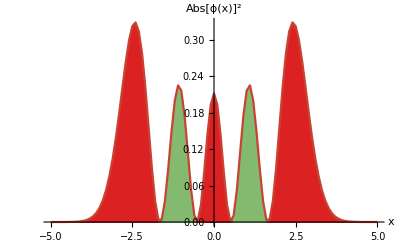

```mathematica
plotDiscreteψ[eigfuncs[[5]], grid]
```